```mathematica
Quit[]
```

```mathematica
Hat[r_]:=Module[{rHat},rHat={{0,-r[[3,1]],r[[2,1]]},{r[[3,1]],0,-r[[1,1]]},{-r[[2,1]],r[[1,1]],0}};
Return[rHat];]

UnHat[rHat_]:=Module[{r},r={{rHat[[3,2]]},{rHat[[1,3]]},{rHat[[2,1]]}};
Return[r];]

UnHat3D[VHat_]:=
	Module[{V},
	V=Join[UnHat[VHat[[1;;3,1;;3]]],{VHat[[1;;3,4]]}ᵀ];
		Return[V];]

Homogenize[rNonHomog_]:=
Module[{rHomog},
rHomog = Join[rNonHomog,{{1}}];
Return[rHomog];]

NonHomogenize[rHomog_]:=
Module[{rNonHomog},
rNonHomog=Drop[rHomog,-1];
Return[rNonHomog];]
```

```mathematica
Only Rotations, Using Euler Lagrange Energy Method:
```

Rx = (1 | 0 | 0
0 | cos(ψ(t)) | -sin(ψ(t))
0 | sin(ψ(t)) | cos(ψ(t)))

Ry = (cos(ϕ(t)) | 0 | sin(ϕ(t))
0 | 1 | 0
-sin(ϕ(t)) | 0 | cos(ϕ(t)))

Rz = (cos(θ(t)) | -sin(θ(t)) | 0
sin(θ(t)) | cos(θ(t)) | 0
0 | 0 | 1)

g_wb = (cos(θ(t)) cos(ϕ(t)) | -cos(ϕ(t)) sin(θ(t)) | sin(ϕ(t)) | 0
cos(ψ(t)) sin(θ(t))+cos(θ(t)) sin(ϕ(t)) sin(ψ(t)) | cos(θ(t)) cos(ψ(t))-sin(θ(t)) sin(ϕ(t)) sin(ψ(t)) | -cos(ϕ(t)) sin(ψ(t)) | 0
sin(θ(t)) sin(ψ(t))-cos(θ(t)) cos(ψ(t)) sin(ϕ(t)) | cos(ψ(t)) sin(θ(t)) sin(ϕ(t))+cos(θ(t)) sin(ψ(t)) | cos(ϕ(t)) cos(ψ(t)) | 0
0 | 0 | 0 | 1)

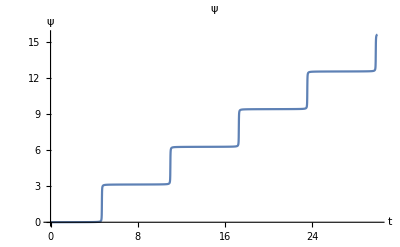

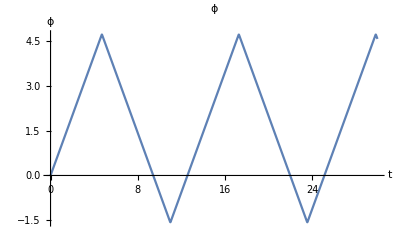

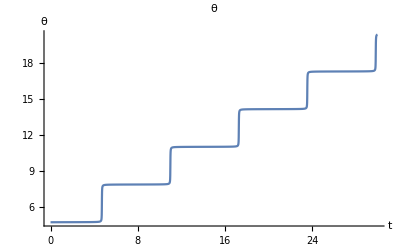

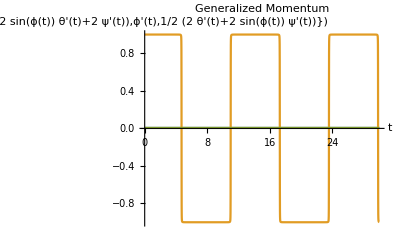

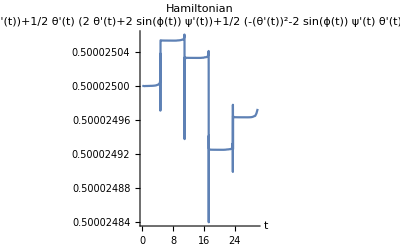

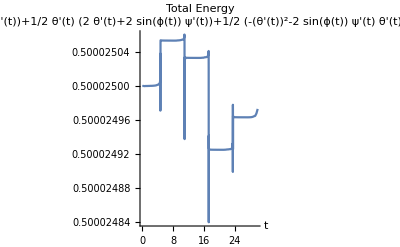

```mathematica
(*CONFIGURATION VARIABLES 3D: *)
(*If both translation and rotation*)
(*q={ {x[t]},{y[t]},{z[t]},{ψ[t]},{ϕ[t]},{θ[t]}};*)
q={{ψ[t]},{ϕ[t]},{θ[t]}};
(*FIRST AND SECOND TIME DERIVATIVES: *)
dq = D[q, t];
ddq = D[dq, t];

(*ROTATION ABOUT X AXIS: *)
ωx = {1,0,0};
Rx = RotationMatrix[ψ[t], ωx];
Print["Rx = " ,Rx]
(*ROTATION ABOUT Y AXIS: *)
ωy = {0,1,0};
Ry = RotationMatrix[ϕ[t], ωy];
Print["Ry = ", Ry]
(*ROTATION ABOUT Z AXIS: *)
ωz = {0,0,1};
Rz = RotationMatrix[θ[t], ωz];
Print["Rz = " ,Rz]
R = Rx.Ry.Rz;
(*p = {{x[t]},{y[t]},{z[t]}};*)
p = {{0},{0},{0}};
T = Join[Join[Rᵀ,pᵀ]ᵀ, {{0,0,0,1}}];
Tdot = D[T, t];
Print["g_wb = ", T]
(*BODY VELOCITIES: *)
V= UnHat3D[Inverse[T].Tdot];

(*Intertia Tensors*)
Ix=(1/12)*m*(yd^2+zd^2);
Iy=(1/12)*m*(zd^2+xd^2);
Iz=(1/12)*m*(xd^2+yd^2);
ℐ= {{Ix, 0, 0},{0, Iy, 0},{0,0, Iz}};
(*TO DO ::: ROTATIONAL INERTIA*)
(*
r={{x},{y},{z}};
rhat = Hat[r];
ℐ =∫_-h^h ∫_-w^w ∫_-l^l ρ*( rhat)ᵀ.( rhat )ⅆxⅆyⅆz;*)


G = Join[Join[m*IdentityMatrix[3],ConstantArray[0,{3,3}]]ᵀ, Join[ConstantArray[0,{3,3}],ℐ]ᵀ];

(*KINETIC ENERGY: *)
KE = 1/2*Vᵀ.G.V;
KE = 1/2*Subscript[V, b] ᵀ.Subscript[g, wb].Subscript[V, b];

(*TODO::: FIX INERTIAL FRAME: *)
CM =  {{0},{0},{0}};
rW = NonHomogenize[T.Homogenize[CM]];

(*POTENTIAL ENERGY: *)
PE = m*g*rW[[3]];

(*LAGRANGIAN: *)
Lag = KE - PE//FullSimplify;
(*Generalized momentum*)
p = D[Lag, dqᵀ];

(*AngularMomentum = {{ Ix*Derivative[1][θx]},{Iy*Derivative[1][θy]},{Iz*Derivative[1][θz]}}*)

(*Hamiltonian*)
TotalEnergy = KE + PE;
Ham = p.dq-Lag;

(*CONSTRAINTS: *)

(*EXTERNAL FORCES: *)

(*IMPACT LAWS: *)

(*EULER LAGRANGE EQUATIONS: *)
Eq1 = D[D[Lag, dq[[1]]],t]-D[Lag, q[[1]]] ==0;
Eq2 = D[D[Lag, dq[[2]]],t]-D[Lag, q[[2]]] ==0;
Eq3 = D[D[Lag, dq[[3]]],t]-D[Lag, q[[3]]] == 0;

(*FIND EQUTIONS OF MOTION: *)
ELtemp = Solve[Eq1&& Eq2 && Eq3,Flatten[{ddq}]];


(*PARAMETERS: *)
m=1;
xd=1;
yd=2;
zd=3;
g=9.81;
ρ = 1;
l = xd/2;
h = zd/2;
w = yd/2;

(*INITIAL CONDITIONS: *)
InitConX= {
ψ[0]==0,
ϕ[0]==0,
θ[0]==3*(Pi/2),
Derivative[1][ψ][0]== 1,
Derivative[1][ϕ][0]==0.005,
Derivative[1][θ][0]==0.005};

InitConY= {
ψ[0]==0,
ϕ[0]==0,
θ[0]==3*(Pi/2),
Derivative[1][ψ][0]==0.005,
Derivative[1][ϕ][0]==1,
Derivative[1][θ][0]==0.005};

InitConZ= {
ψ[0]==0,
ϕ[0]==0,
θ[0]==3*(Pi/2),
Derivative[1][ψ][0]==0.0005,
Derivative[1][ϕ][0]==0.0005,
Derivative[1][θ][0]==1};

EL = {ψ''[t]==ELtemp[[1,1,2]], ϕ''[t]==ELtemp[[1,2,2]], θ''[t]==ELtemp[[1,3,2]]};
(*NUMERICAL SOLUTIONS: *)
sol = NDSolve[Join[EL, InitConY],{ψ,ϕ,θ,ψ',ϕ',θ'},{t,0,30}];

(*ANIMATION: *)
ψsol=ψ[t]/.sol[[1]];
ϕsol=ϕ[t]/.sol[[1]];
θsol=θ[t]/.sol[[1]];
psol =  p/.sol[[1]];
Hamsol = Ham/.sol;
TotEnersol = TotalEnergy /.sol;

Plot[ψsol,{t,0,30},AxesLabel->{t,ψ},PlotLabel->"ψ"]
Plot[ϕsol,{t,0,30},AxesLabel->{t,ϕ},PlotLabel->"ϕ"]
Plot[θsol,{t,0,30},AxesLabel->{t,θ},PlotLabel->"θ"]
Plot[psol,{t,0,30},AxesLabel->{t,p},PlotLabel->"Generalized Momentum"]
Plot[Hamsol,{t,0,30},AxesLabel->{t,Ham},PlotLabel->"Hamiltonian"]
Plot[TotEnersol,{t,0,30},AxesLabel->{t,Ham},PlotLabel->"Total Energy"]

Ψ[τ_]:=ψsol/.t-> τ;
Φ[τ_]:=ϕsol/.t-> τ;
Θ[τ_]:=θsol/.t-> τ;

Animate[Graphics3D[Rotate[Rotate[Rotate[{Arrowheads[0.04],Red,Arrow[Tube[{{0,0,0},{2,0,0}}]],Green,Arrow[Tube[{{0,0,0},{0,2.5,0}}]],Blue,Arrow[Tube[{{0,0,0},{0,0,3}}]],Purple,Cuboid[{-(xd/2),-(yd/2),-(zd/2)},{xd/2,yd/2,zd/2}]},Ψ[τ],{1,0,0}],Φ[τ],{0,1,0}],Θ[τ],{0,0,1}],PlotRange->3,Axes->False,Boxed->True,Lighting->"Neutral", PlotLabel->"Principal Axis of Maximum Inertia Animation: Stable Rotation"],{τ,0,30}]
```

```mathematica
Rotations, Using Euler Equations:
```

{{θx→InterpolatingFunction[{{0., 30.}}, <>],θy→InterpolatingFunction[{{0., 30.}}, <>],θz→InterpolatingFunction[{{0., 30.}}, <>]}}

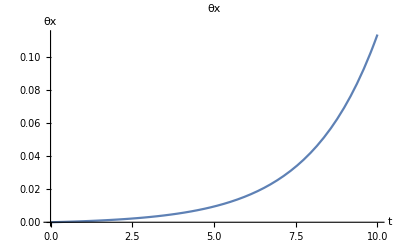

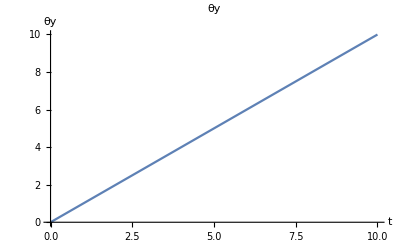

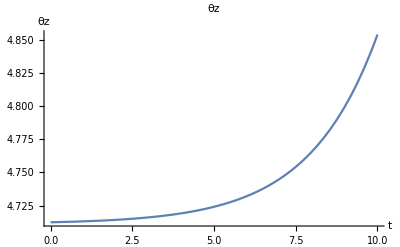

{{θx→InterpolatingFunction[{{0., 30.}}, <>],θy→InterpolatingFunction[{{0., 30.}}, <>],θz→InterpolatingFunction[{{0., 30.}}, <>]}}

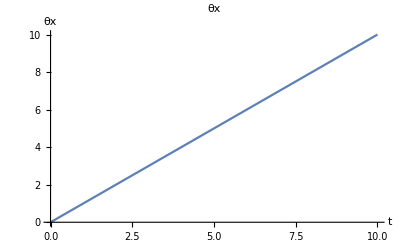

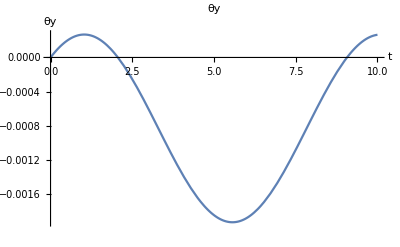

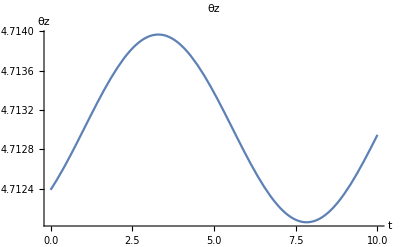

{{θx→InterpolatingFunction[{{0., 30.}}, <>],θy→InterpolatingFunction[{{0., 30.}}, <>],θz→InterpolatingFunction[{{0., 30.}}, <>]}}

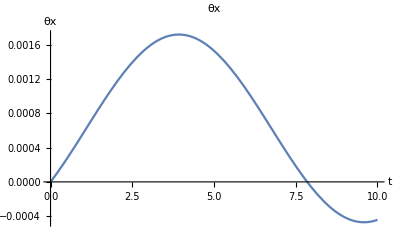

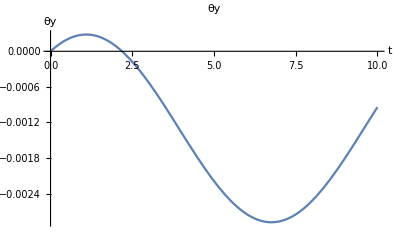

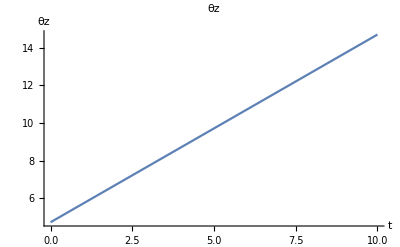

```mathematica
m=1;xd=1;yd=2;zd=3;Ix=(1/12)*m*(yd^2+zd^2);
Iy=(1/12)*m*(zd^2+xd^2);Iz=(1/12)*m*(xd^2+yd^2);
(*Intermediate Axis of Inertia is Iy*)
(*If rotation about Ix and Iz is perterbed slightly, the rotation is still stable, but if rotation about Iy is perterbed slightly, it will go unstable*)

(*Principle Axis of Intermediate Inertia Animation: Iy*)
soln=NDSolve[{Ix*Derivative[2][θx][t]==(Iy-Iz)*Derivative[1][θy][t]*Derivative[1][θz][t],Iy*Derivative[2][θy][t]==(Iz-Ix)*Derivative[1][θz][t]*Derivative[1][θx][t],Iz*Derivative[2][θz][t]==(Ix-Iy)*Derivative[1][θx][t]*Derivative[1][θy][t],θx[0]==0,θy[0]==0,θz[0]==3*(Pi/2),Derivative[1][θx][0]==0.0005,Derivative[1][θy][0]==1,Derivative[1][θz][0]==0.0005},{θx,θy,θz},{t,0,30}]

ax[t_]:=Evaluate[θx[t]/.soln[[1,1]]]
ay[t_]:=Evaluate[θy[t]/.soln[[1,2]]]
az[t_]:=Evaluate[θz[t]/.soln[[1,3]]]

Animate[Graphics3D[Rotate[Rotate[Rotate[{Arrowheads[0.04],Red,Arrow[Tube[{{0,0,0},{2,0,0}}]],Green,Arrow[Tube[{{0,0,0},{0,2.5,0}}]],Blue,Arrow[Tube[{{0,0,0},{0,0,3}}]],Purple,Cuboid[{-(xd/2),-(yd/2),-(zd/2)},{xd/2,yd/2,zd/2}]},ax[t],{1,0,0}],ay[t],{0,1,0}],az[t],{0,0,1}],PlotRange->3,Axes->False,Boxed->True,Lighting->"Neutral", PlotLabel->"Principle Axis of Intermediate Inertia Animation: Unstable Rotation"],{t,0,30}]

Plot[Evaluate[θx[t]/.soln[[1,1]]],{t,0,10},AxesLabel->{t,θx},PlotLabel->"θx"]
Plot[Evaluate[θy[t]/.soln[[1,2]]],{t,0,10},AxesLabel->{t,θy},PlotLabel->"θy"]
Plot[Evaluate[θz[t]/.soln[[1,3]]],{t,0,10},AxesLabel->{t,θz},PlotLabel->"θz"]

(*Principle Axis of Maximum Inertia Animation: Ix*)
soln2=NDSolve[{Ix*Derivative[2][θx][t]==(Iy-Iz)*Derivative[1][θy][t]*Derivative[1][θz][t],Iy*Derivative[2][θy][t]==(Iz-Ix)*Derivative[1][θz][t]*Derivative[1][θx][t],Iz*Derivative[2][θz][t]==(Ix-Iy)*Derivative[1][θx][t]*Derivative[1][θy][t],θx[0]==0,θy[0]==0,θz[0]==3*(Pi/2),Derivative[1][θx][0]==1,Derivative[1][θy][0]==0.0005,Derivative[1][θz][0]==0.0005},{θx,θy,θz},{t,0,30}]

ax2[t_]:=Evaluate[θx[t]/.soln2[[1,1]]]
ay2[t_]:=Evaluate[θy[t]/.soln2[[1,2]]]
az2[t_]:=Evaluate[θz[t]/.soln2[[1,3]]]

Animate[Graphics3D[Rotate[Rotate[Rotate[{Arrowheads[0.04],Red,Arrow[Tube[{{0,0,0},{2,0,0}}]],Green,Arrow[Tube[{{0,0,0},{0,2.5,0}}]],Blue,Arrow[Tube[{{0,0,0},{0,0,3}}]],Purple,Cuboid[{-(xd/2),-(yd/2),-(zd/2)},{xd/2,yd/2,zd/2}]},ax2[t],{1,0,0}],ay2[t],{0,1,0}],az2[t],{0,0,1}],PlotRange->3,Axes->False,Boxed->True,Lighting->"Neutral", PlotLabel->"Principal Axis of Maximum Inertia Animation: Stable Rotation"],{t,0,30}]

Plot[Evaluate[θx[t]/.soln2[[1,1]]],{t,0,10},AxesLabel->{t,θx},PlotLabel->"θx"]
Plot[Evaluate[θy[t]/.soln2[[1,2]]],{t,0,10},AxesLabel->{t,θy},PlotLabel->"θy"]
Plot[Evaluate[θz[t]/.soln2[[1,3]]],{t,0,10},AxesLabel->{t,θz},PlotLabel->"θz"]

(*Principle Axis of Minimum Inertia Animation: Iz*)
soln3=NDSolve[{Ix*Derivative[2][θx][t]==(Iy-Iz)*Derivative[1][θy][t]*Derivative[1][θz][t],Iy*Derivative[2][θy][t]==(Iz-Ix)*Derivative[1][θz][t]*Derivative[1][θx][t],Iz*Derivative[2][θz][t]==(Ix-Iy)*Derivative[1][θx][t]*Derivative[1][θy][t],θx[0]==0,θy[0]==0,θz[0]==3*(Pi/2),Derivative[1][θx][0]==0.0005,Derivative[1][θy][0]==0.0005,Derivative[1][θz][0]==1},{θx,θy,θz},{t,0,30}]

ax3[t_]:=Evaluate[θx[t]/.soln3[[1,1]]]
ay3[t_]:=Evaluate[θy[t]/.soln3[[1,2]]]
az3[t_]:=Evaluate[θz[t]/.soln3[[1,3]]]

Animate[Graphics3D[Rotate[Rotate[Rotate[{Arrowheads[0.04],Red,Arrow[Tube[{{0,0,0},{2,0,0}}]],Green,Arrow[Tube[{{0,0,0},{0,2.5,0}}]],Blue,Arrow[Tube[{{0,0,0},{0,0,3}}]],Purple,Cuboid[{-(xd/2),-(yd/2),-(zd/2)},{xd/2,yd/2,zd/2}]},ax3[t],{1,0,0}],ay3[t],{0,1,0}],az3[t],{0,0,1}],PlotRange->3,Axes->False,Boxed->True,Lighting->"Neutral", PlotLabel-> "Principal Axis of Minimum Inertia Animation: Stable Rotation"],{t,0,30}]

Plot[Evaluate[θx[t]/.soln3[[1,1]]],{t,0,10},AxesLabel->{t,θx},PlotLabel->"θx"]
Plot[Evaluate[θy[t]/.soln3[[1,2]]],{t,0,10},AxesLabel->{t,θy},PlotLabel->"θy"]
Plot[Evaluate[θz[t]/.soln3[[1,3]]],{t,0,10},AxesLabel->{t,θz},PlotLabel->"θz"]
```